```mathematica
(* C3.AI COVID CHALLENGE *)
```

```mathematica
(* Sweden *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
type = "Deaths_per_Million";
policy = "C6_Policy";
```

```mathematica
pD0 = 0.6649;
pD1=0.1373;
pD2=0.0598;
pD3=0.1188;
pD4=0.0192;
```

```mathematica
(* COnditional Prob *)
```

```mathematica
pD0C6l1=0.7830;
pD1C6l1=0.9973;
pD2C6l1 = 0.9938;
pD3C6l1=0.9969;
pD4C6l1=0.9808;
```

```mathematica
pD0C6l0=1-pD0C6l1;
pD1C6l0=1-pD1C6l1;
pD2C6l0 =1-pD2C6l1;
pD3C6l0=1-pD3C6l1;
pD4C6l0=1-pD4C6l1;
```

```mathematica
(* C6 - 1 *)
```

```mathematica
prC6l0 = pD0 pD0C6l0 +  pD1 pD1C6l0+ pD2 pD2C6l0+ pD3 pD3C6l0+ pD4 pD4C6l0
```

0.145762

```mathematica
prC6l1= pD0 pD0C6l1 +  pD1 pD1C6l1+ pD2 pD2C6l1+ pD3 pD3C6l1+ pD4 pD4C6l1
```

0.854238

```mathematica
(* Quantum Prob *)
```

```mathematica
interfC6l0 = Sqrt[pD0 pD0C6l0 pD1 pD1C6l0]Cos[θ00-θ10]+ Sqrt[pD0 pD0C6l0  pD2 pD2C6l0] Cos[θ00-θ20] +  Sqrt[pD0 pD0C6l0  pD3 pD3C6l0] Cos[θ00-θ30]+ Sqrt[ pD0 pD0C6l0  pD4 pD4C6l0] Cos[θ00-θ40]+ 
Sqrt[pD1 pD1C6l0  pD2 pD2C6l0 ] Cos[θ10-θ20]+ Sqrt[pD1 pD1C6l0  pD3 pD3C6l0] Cos[θ10-θ30]+Sqrt[pD1 pD1C6l0  pD4 pD4C6l0 ]Cos[θ10-θ40]+
Sqrt[pD2 pD2C6l0  pD3 pD3C6l0]  Cos[θ20-θ30]+ Sqrt[pD2 pD2C6l0  pD4 pD4C6l0 ]Cos[θ20-θ40]+Sqrt[pD3 pD3C6l0  pD4 pD4C6l0 ]Cos[θ30-θ40];
```

```mathematica
interfC6l1 = Sqrt[pD0 pD0C6l1 pD1 pD1C6l1]Cos[θ01-θ11]+ Sqrt[pD0 pD0C6l1 pD2 pD2C6l1] Cos[θ01-θ21] +  Sqrt[pD0 pD0C6l1  pD3 pD3C6l1] Cos[θ01-θ31]+ Sqrt[ pD0 pD0C6l1  pD4 pD4C6l1] Cos[θ01-θ41]+ 
Sqrt[pD1 pD1C6l1  pD2 pD2C6l1 ] Cos[θ11-θ21]+ Sqrt[pD1 pD1C6l1  pD3 pD3C6l1] Cos[θ11-θ31]+Sqrt[pD1 pD1C6l1 pD4 pD4C6l1] Cos[θ11-θ41]+
Sqrt[pD2 pD2C6l1  pD3 pD3C6l1 ] Cos[θ21-θ31]+ Sqrt[pD2 pD2C6l1  pD4 pD4C6l1] Cos[θ21-θ41]+Sqrt[pD3 pD3C6l1  pD4 pD4C6l1] Cos[θ30-θ41];
```

```mathematica
qprC6l0 = prC6l0 + 2 interfC6l0;
```

```mathematica
qprC6l1= prC6l1 + 2 interfC6l1;
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
(*FullSimplify[qprC6l1/(qprC6l0+qprC6l1)]; *)
```

```mathematica
res = Minimize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```

{0.0270547,{θ00→3.12584,θ01→-0.0157531,θ10→-0.0157536,θ20→-0.0157537,θ30→-0.0157535,θ40→-0.0157536,θ11→-0.0157531,θ21→-0.0157531,θ31→-0.0157531,θ41→-0.0157532}}

```mathematica
(* Params *)
```

```mathematica
θ10=res[[2]][[3]][[2]];
 θ20=res[[2]][[4]][[2]];
 θ30=res[[2]][[5]][[2]];
θ40=res[[2]][[6]][[2]];
θ11=res[[2]][[7]][[2]];
θ21=res[[2]][[8]][[2]];
θ31=res[[2]][[9]][[2]];
θ41=res[[2]][[10]][[2]];
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
```

```mathematica
(* Updated probabilities *)
```

```mathematica
{qprC6l0Norm,qprC6l1Norm}
```

{(10.3023+4.00665 Cos[θ00]-0.0631243 Sin[θ00])/(128.284+4.00665 Cos[θ00]+108.392 Cos[θ01]-0.0631243 Sin[θ00]-1.70765 Sin[θ01]),1-(10.3023+4.00665 Cos[θ00]-0.0631243 Sin[θ00])/(128.284+4.00665 Cos[θ00]+108.392 Cos[θ01]-0.0631243 Sin[θ00]-1.70765 Sin[θ01])}

```mathematica
p0 = Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p1 =  Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
Show[p0,p1]
```

-Graphics3D-

```mathematica
fig = StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

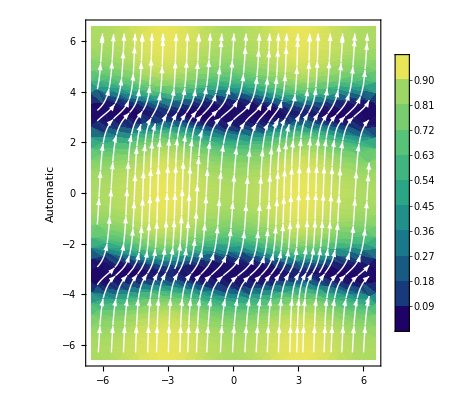

```mathematica
Clear[ θ10,θ20, θ30,θ40, θ11, θ21, θ31, θ41]
```

```mathematica
res = Maximize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```

{0.599076,{θ00→-0.0157536,θ01→-3.15735,θ10→-1.04233,θ20→-1.18342,θ30→-1.33467,θ40→-1.14213,θ11→-1.55531,θ21→0.112742,θ31→-1.76147,θ41→0.183178}}

```mathematica
(* Params *)
```

```mathematica
θ10=res[[2]][[3]][[2]];
 θ20=res[[2]][[4]][[2]];
 θ30=res[[2]][[5]][[2]];
θ40=res[[2]][[6]][[2]];
θ11=res[[2]][[7]][[2]];
θ21=res[[2]][[8]][[2]];
θ31=res[[2]][[9]][[2]];
θ41=res[[2]][[10]][[2]];
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
```

```mathematica
(* Updated probabilities *)
```

```mathematica
{qprC6l0Norm,qprC6l1Norm}
```

{(10.264+1.52967 Cos[θ00]-3.66558 Sin[θ00])/(84.8298+1.52967 Cos[θ00]+31.3413 Cos[θ01]-3.66558 Sin[θ00]-64.6681 Sin[θ01]),1-(10.264+1.52967 Cos[θ00]-3.66558 Sin[θ00])/(84.8298+1.52967 Cos[θ00]+31.3413 Cos[θ01]-3.66558 Sin[θ00]-64.6681 Sin[θ01])}

```mathematica
p0 = Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p1 =  Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
Show[p0,p1]
```

-Graphics3D-

```mathematica
fig = StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```